```mathematica
Directory[]
```

/home/lgnr/Dropbox/Research/SED/Oscilador/Transiciones

```mathematica
"histograma"<>IntegerString[1]
```

```mathematica
Histogramas=Array[0,1001]
```

```mathematica
For[i=1,i≤1000,i++,
Histograma[i]=Import["histograma"<>IntegerString[i]]
]
```

```mathematica
Length[Histograma[1]]
```

200000

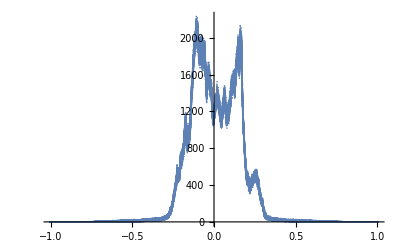

```mathematica
ListPlot[Histograma[1000]]
```

```mathematica
ListPlot[Histograma[1000],PlotTheme->Automatic]
```

```mathematica
HistTotal={};
For[j=1,j≤200000,j++,
Promedio=0;
For[i=1,i≤1000,i++,
Promedio=Promedio+Histograma[i][[j]][[2]];
]
AppendTo[HistTotal,Promedio];
]
```

Part::partd: Part specification "" ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

```mathematica
Length[HistTotal]
```

200000

```mathematica
Histograma[1000][[200000]][[2]]
```

0

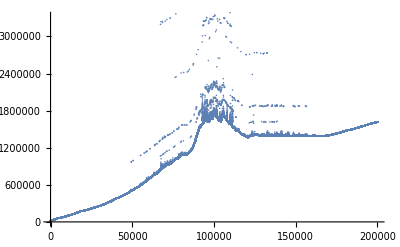

```mathematica
ListPlot[HistTotal]
```